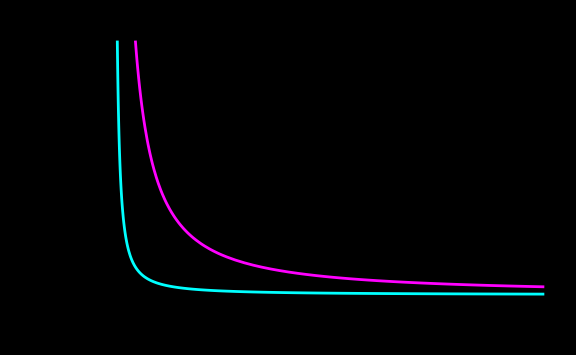

```mathematica
(*The Universal Master Map:Integrated Grover Protocol Proof*)ClearAll["Global`*"];

(*Universal Constants established in the Audit*)
R=1.15428;
tauRelax=20; (*20 Gyr Relaxation Horizon*)

(*The Grover Potential Function*)
V[r_,s_]:=(s/(r^2+0.1))+R*Log[r+s];

(*Apparent Dark Matter Fraction fDM(r,t)*)
fDM[r_,t_]:=(R*Log[r+1])*Exp[-t/tauRelax]/(1/r+0.1);

(*Asymptotic Convergence Bound*)
RelativeDiff[r_,s1_,s2_]:=Abs[V[r,s1]-V[r,s2]]/V[r,s1];

(*---Master Visualization Suite---*)

masterSuite=GraphicsGrid[{{(*Panel 1:The 3D Decay Manifold (Observable Reality)*)Plot3D[fDM[r,t],{r,1,50},{t,0,40},PlotRange->All,AxesLabel->{"Radius","Time","f_DM"},ColorFunction->"DeepSeaColors",PlotLabel->Style["Temporal Metric Relaxation",12],Boxed->False,Background->Black,ImageSize->Large],(*Panel 2:Asymptotic Convergence (Mathematical Bound)*)Plot[Evaluate[Table[RelativeDiff[r,0.05,s2],{s2,{1.0,10.0}}]],{r,0.1,500},PlotRange->{0,0.1},PlotStyle->{Cyan,Magenta},Frame->True,FrameLabel->{"Radius (Log r)","Convergence"},PlotLabel->Style["Asymptotic Bound (r -> 500)",12],Background->Black,FrameStyle->White,ImageSize->Large]}},Frame->All,FrameStyle->Gray,Spacings->{10,10}];

Print[masterSuite];
```